# Моделирование COVID-19 над Ботсваной

## COVID-19 simulations over Botswana

Антон Антонов
MathematicaForPrediction at WordPress
SystemModeling at GitHub
April 2020
June 2023

## Введение

В этом блокноте мы используем данные Ботсваны для моделирования распространения COVID-19. 
Представленная модель является минимально жизнеспособным вычислительным приложением для моделирования и аналитики.
Цель этого приложения - облегчить многократное выполнение с различными сценариями развития событий.
Целевым конечным пользователем является президентская целевая группа COVID-19 в Ботсване.

## Многоуровневый подход

-Graphics3D-

## Основные моменты пространственной модели

### Слой популяций

Модель одного сайта

Модель с несколькими сайтами

Подготовка данных

Ввод и подготовка данных

Визуализация данных:

Гистограммы

Хекстильная гистограмма

Хекстильбины

Социальные сети

График WhattsStrogratz

График сообщества

График соседей

### Уровень мобильности

Дорожная мобильность

Воздушная мобильность

Железнодорожная мобильность

Пантонная мобильность

## Данные по Ботсване

Данные о городах Ботсваны и их населении были получены с помощью функции CitiData системы Mathematica.

```mathematica
dsBotswanaCityRecords=ResourceFunction["ImportCSVToDataset"]["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Data/dfBotswanaCityRecords.csv"]
```

#### Сводка данных

```mathematica
ResourceFunction["RecordsSummary"][dsBotswanaCityRecords]
```

## Подготовка данных

### Население

Подготовьте данные о городе в виде пар "координаты-значения" (ассоциации):

```mathematica
aPopulations=Association@Map[{#Lon,#Lat}->#Population&,Normal[dsBotswanaCityRecords]];
```

```mathematica
aPopulations⟦1;;3⟧
```

Установите число зараженных 22 в месте Габороне:

```mathematica
aInfected=AssociationThread[Keys[aPopulations],0];
aInfected=Join[aInfected,<|{25.91,-24.65}->16,{27.5,-21.17}->1,{25.51,-24.4}->5|>];
```

Один погибший (в Габороне):

```mathematica
aDead=AssociationThread[Keys[aPopulations],0];
aDead=Join[aDead,<|{25.91,-24.65}->1|>];
```

### Количество больничных мест

Общая численность населения из данных по городу, полученных выше:

```mathematica
Total[aPopulations]
```

Общая численность населения из базы данных CountryData:

```mathematica
CountryData["Botswana","Population"]
```

```mathematica
(*aHospitalBeds=Association@Map[{#Longitude,#Latitude}->#["Hospital Beds"]&,Normal@aBWADatasets["Stocks"][Select[NumberQ[#["Hospital Beds"]]&]]]*)
```

```mathematica
aHospitalBeds=<|{28.428,-21.9814}->38.,{27.5,-21.17}->589.,{25.91,-24.65}->681.,{21.6482,-21.6961}->96.,{25.4319,-25.4742}->58.,{22.1549,-19.3562}->34.,{25.2541,-20.2112}->50.,{25.55,-25.42}->55.,{25.5629,-25.347}->167.,{25.15,-17.81}->33.,{25.5859,-21.4096}->24.,{25.68,-25.22}->472.,{26.48,-22.95}->320.,{27.4167,-20.6667}->55.,{23.4181,-19.9953}->340.,{25.8108,-24.5551}->146.,{27.7514,-21.8811}->55.,{26.2305,-24.197}->181.,{25.51,-24.4}->346.,{25.4023,-21.312}->106.,{27.1147,-22.5515}->75.,{25.864,-24.8706}->163.,{24.3995,-21.03}->42.,{27.529,-23.0308}->56.,{27.83,-21.98}->172.,{26.71,-22.39}->370.,{25.5326,-24.6664}->61.,{22.4113,-26.0208}->57.,{27.4,-21.33}->44.,{21.7495,-23.9931}->70.,{25.331,-24.2438}->42.|>;
```

## Картографирование страны Ботсвана

```mathematica
GeoHistogram[KeyMap[Reverse,aPopulations],Quantity[112,"Kilometers"]]
```

```mathematica
Show[{HextileHistogram[aPopulations,1,PlotRange->All],Graphics[MapIndexed[Text[#2⟦1⟧,#1]&,Sort@Keys@HextileBins[Keys[aPopulations],1,"PolygonKeys"->False]]]}]
```

## Применение эпидемиологических моделей к слоям населения и мобильности

### SIR Модель

```mathematica
ModelGridTableForm[SIRModel[t]]
```

### SEI2HR (Наша адаптация модели SEIR)

```mathematica
SEI2HRModel[t]
```

```mathematica
ModelGridTableForm[SEI2HRModel[t]]
```

## Модель одного объекта

```mathematica
modelSEI2HREcon=SEI2HREconModel[t,"InitialConditions"->True,"RateRules"->True,"TotalPopulationRepresentation"->"AlgebraicEquation"];
```

```mathematica
modelSEI2HREcon//ModelGridTableForm
```

## Данные по настройке (один сайт)

### Установка всей Ботсваны (все объекты объединены вместе)

```mathematica
Total[aPopulations]
```

```mathematica
population=QuantityMagnitude[CountryData["Botswana","Population"]]
```

```mathematica
numberOfHospitalBeds=Total[aHospitalBeds]
```

```mathematica
numberOfInfected=Total[aInfected]
```

```mathematica
numberOfDead=Total[aDead]
```

### Установка только для Габороне

Мы знаем, что Габороне - самый большой город:

```mathematica
TakeLargest[aPopulations,1]
```

```mathematica
population=First@TakeLargest[aPopulations,1]
```

```mathematica
numberOfHospitalBeds=aHospitalBeds[First@Keys[TakeLargest[aPopulations,1]]]
```

```mathematica
numberOfInfected=aInfected[First@Keys[TakeLargest[aPopulations,1]]]
```

```mathematica
numberOfDead=aDead[First@Keys[TakeLargest[aPopulations,1]]]
```

### Установка для Большого Габороне (сайт)

Взяв за основу многосайтовую модель, в которой есть Габороне:

```mathematica
aCityData=Association@Map[{#Lon,#Lat}->{#City,#Population}&,Normal[dsBotswanaCityRecords]];
```

```mathematica
aPolygonToData2=HextileBins[aCityData,1,"AggregationFunction"->(Prepend[##,{"Total",Total[(##)⟦All,2⟧]}]&)];
Length[aPolygonToData2]
```

```mathematica
pos=First[Position[Values[aPolygonToData2],"Gaborone",∞]]
```

```mathematica
aPolygonToData2⟦Sequence@@Rest[pos]⟧
```

```mathematica
Values[aPolygonToData2]⟦First@pos⟧
```

```mathematica
population=%⟦1,2⟧
```

```mathematica
KeySelect[aHospitalBeds,RegionMember[Keys[aPolygonToData2]⟦First@pos⟧,#]&]
```

```mathematica
numberOfHospitalBeds=Total[%]
```

```mathematica
numberOfInfected=aInfected[First@Keys[TakeLargest[aPopulations,1]]]
```

```mathematica
numberOfDead=aDead[First@Keys[TakeLargest[aPopulations,1]]]
```

## Установите начальные условия и значения скорости (один сайт)

```mathematica
modelSEI2HREcon=SetInitialConditions[modelSEI2HREcon,<|TP[0]->population,HB[0]->numberOfHospitalBeds,INSP[0]->numberOfInfected,DIP[0]->1,SP[0]->population-(numberOfDead+numberOfInfected)|>];
```

Назначение общих значений тарифов:

```mathematica
modelSEI2HREcon=
SetRateRules[modelSEI2HREcon,
<|mspr[HB]->10^6,msdp[HB]->0.1,mscr[TP]->1,mscr[ISSP]->1,mscr[INSP]->1,mscr[HP]->1,κ[HMS]->10^6,κ[MS]->10^6,κ[MSD]->10^6,
β[ISSP]->0.5*Piecewise[{{1,t<qsd},{qcrf,qsd≤t≤qsd+ql}},1],
β[INSP]->0.5*Piecewise[{{1,t<qsd},{qcrf,qsd≤t≤qsd+ql}},1],
qsd->60,
ql->8*7,
qcrf->0.25,
μ[TP]->0.006406/365,
μ[ISSP]->0.0005/aip,
μ[INSP]->0.0005/aip,
μ[HP]->0.1*μ[ISSP]
|>];
```

## Интерфейс (один сайт)

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->400};
lsPopulationKeys={TP,SP,EP,ISSP,INSP,HP,RP,DIP,HB};
lsSuppliesKeys={MS,MSD,HMS};
lsMoneyKeys={MHS,MLP,MMSP};
Manipulate[
DynamicModule[{modelLocal=modelSEI2HREcon,aStocks=modelSEI2HREcon["Stocks"],aSolLocal=aParSol,lsPopulationPlots,lsMoneyPlots,lsSuppliesPlots},

modelLocal=SetRateRules[modelLocal,<|aincp->aincpM,aip->aipM,sspf[SP]->sspfM,β[HP]->crhpM,qsd->qsdM,ql->qlM,qcrf->qcrfM,nhbr[TP]->nhbrM/1000,nhbcr[ISSP,ISNP]->nhbcrM,mspr[HB]->msprM,msdp[HB]->msdpM|>];
aSolLocal=Association[ModelNDSolve[modelLocal,{t,ndays}]⟦1⟧];

lsPopulationPlots=
Quiet@ParametricSolutionsPlots[
aStocks,
KeyTake[aSolLocal,Intersection[lsPopulationKeys,displayPopulationStocks]],
None,ndays,
"LogPlot"->popLogPlotQ,"Together"->popTogetherQ,"Derivatives"->popDerivativesQ,"DerivativePrefix"->"Δ",opts,Epilog->{Gray,Dashed,Line[{{qsdM,0},{qsdM,1.5*population}}],Line[{{qsdM+qlM,0},{qsdM+qlM,1.5*population}}]}];

lsSuppliesPlots=
If[Length[KeyDrop[aSolLocal,Join[lsPopulationKeys,lsMoneyKeys]]]==0,{},
(*ELSE*)
Quiet@ParametricSolutionsPlots[
aStocks,
KeyTake[KeyDrop[aSolLocal,Join[lsPopulationKeys,lsMoneyKeys]],displaySupplyStocks],
None,ndays,
"LogPlot"->supplLogPlotQ,"Together"->supplTogetherQ,"Derivatives"->supplDerivativesQ,"DerivativePrefix"->"Δ",opts]
];

lsMoneyPlots=
Quiet@ParametricSolutionsPlots[
aStocks,
KeyTake[aSolLocal,Intersection[lsMoneyKeys,displayMoneyStocks]],
None,ndays,
"LogPlot"->moneyLogPlotQ,"Together"->moneyTogetherQ,"Derivatives"->moneyDerivativesQ,"DerivativePrefix"->"Δ",opts];

Multicolumn[Join[lsPopulationPlots,lsSuppliesPlots,lsMoneyPlots],nPlotColumns,Dividers->All,FrameStyle->GrayLevel[0.8]],
SaveDefinitions->True
],
{{ndays,365,"Number of days"},1,365,1,Appearance->{"Open"}},
Delimiter,
{{aincpM,6.,"Average incubation period (days)"},1,60.,1,Appearance->{"Open"}},
{{aipM,21.,"Average infectious period (days)"},1,60.,1,Appearance->{"Open"}},
{{sspfM,0.2,"Severely symptomatic population fraction"},0,1,0.025,Appearance->{"Open"}},
{{crhpM,0.1,"Contact rate of the hospitalized population"},0,30,0.1,Appearance->{"Open"}},
Delimiter,
{{qsdM,55,"Quarantine start days"},0,365,1,Appearance->{"Open"}},
{{qlM,8*7,"Quarantine length (in days)"},0,120,1,Appearance->{"Open"}},
{{qcrfM,0.25,"Quarantine contact rate fraction"},0,1,0.01,Appearance->{"Open"}},
Delimiter,
{{nhbrM,2.9,"Number of hospital beds rate (per 1000 people)"},0,100,0.1,Appearance->{"Open"}},
{{nhbcrM,0,"Number of hospital beds change rate"},-0.5,0.5,0.001,Appearance->{"Open"}},
{{msprM,200,"Medical supplies production rate"},0,50000,10,Appearance->{"Open"}},
{{msdpM,1.2,"Medical supplies delivery period"},0,10,0.1,Appearance->{"Open"}},
Delimiter,
{{displayPopulationStocks,lsPopulationKeys,"Population stocks to display:"},lsPopulationKeys,ControlType->TogglerBar},
{{popTogetherQ,True,"Plot populations together"},{False,True}},
{{popDerivativesQ,False,"Plot populations derivatives"},{False,True}},
{{popLogPlotQ,False,"LogPlot populations"},{False,True}},
Delimiter,
{{displaySupplyStocks,lsSuppliesKeys,"Supplies stocks to display:"},lsSuppliesKeys,ControlType->TogglerBar},
{{supplTogetherQ,True,"Plot supplies functions together"},{False,True}},
{{supplDerivativesQ,False,"Plot supplies functions derivatives"},{False,True}},
{{supplLogPlotQ,True,"LogPlot supplies functions"},{False,True}},
Delimiter,
{{displayMoneyStocks,lsMoneyKeys,"Money stocks to display:"},lsMoneyKeys,ControlType->TogglerBar},
{{moneyTogetherQ,True,"Plot money functions together"},{False,True}},
{{moneyDerivativesQ,False,"Plot money functions derivatives"},{False,True}},
{{moneyLogPlotQ,True,"LogPlot money functions"},{False,True}},
{{nPlotColumns,1,"Number of plot columns"},Range[5]},
ControlPlacement->Left,ContinuousAction->False]
```

## "Посевная" модель (многосайтовая)

В этом разделе мы создаем модель "затравки", которая копируется на все ячейки.

Здесь мы создаем объект модели:

```mathematica
model1=SEI2HREconModel[t,"InitialConditions"->True,"RateRules"->True,"TotalPopulationRepresentation"->"AlgebraicEquation"];
```

В дополнение к классической эпидемиологической компартментной модели SIR [Wk1, HH1], выбранная посевная модель имеет население "Hospitalized Population" и ограничивающие запасы ресурсов "Hospital Beds" и "Medical Supplies", [AA6, AA7]:

```mathematica
Magnify[KeyTake[ModelGridTableForm[model1],{"Stocks","Rates"}],0.6]
```

### Стандартные значения

Вот ставки по умолчанию для основной модели:

```mathematica
aDefaultPars=<|
aip->26,
aincp->5,
β[ISSP]->0.5,
β[INSP]->0.5,
β[HP]->0.01,
μ[ISSP]->0.035/aip,
μ[INSP]->0.01/aip,
nhbr[TP]->100/1000,
lpcr[ISSP,INSP]->1,
hscr[ISSP,INSP]->1
|>;
```

### Уровень карантинных сценариев

```mathematica
aQuarantineRates=<|β[ISSP]->0.15,β[INSP]->0.15,β[HP]->0.01|>;
```

## Уровень мобильности

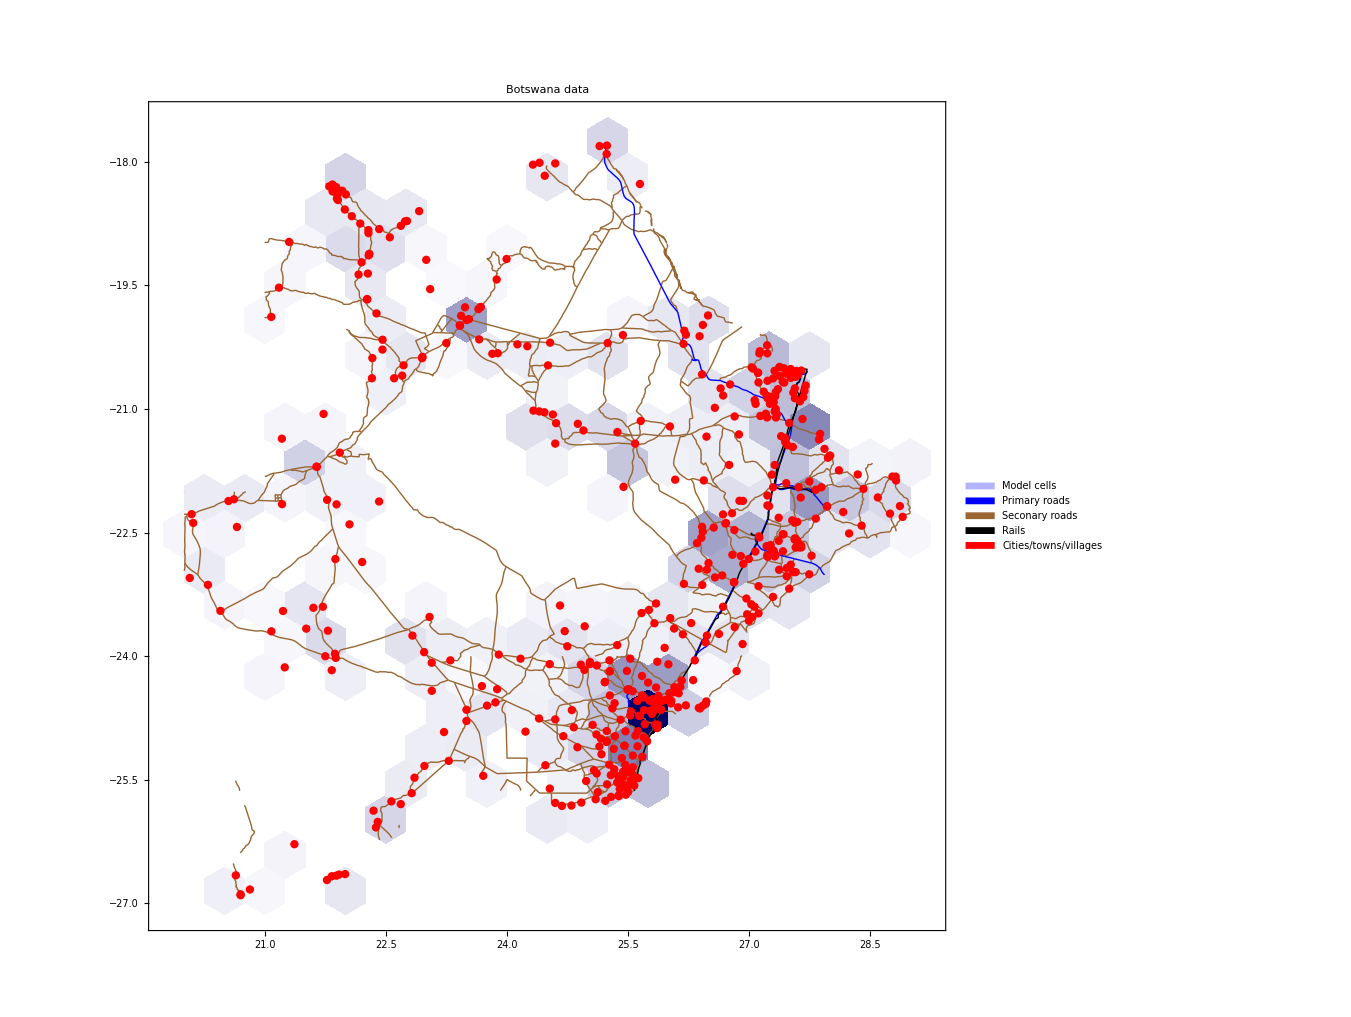

## Моделирование (многосайтовое)

### Параметры

```mathematica
cellRadius=1; (*Geo degrees*)
```

```mathematica
imgSize=Medium;
```

### Установка модели посевного материала

```mathematica
ecmBWA=
ECMMonUnit[]⟹
ECMMonSetSingleSiteModel[model1]⟹
ECMMonEcho[Style["Set default and quarantine rates in the single-site model:",Bold,Purple]]⟹
ECMMonAssignRateRules[Join[aDefaultPars,aQuarantineRates]]⟹
ECMMonEcho[Style["Show the single-site model tabulated form:",Bold,Purple]]⟹
ECMMonEchoFunctionContext[Magnify[KeyTake[ModelGridTableForm[#singleSiteModel],{"InitialConditions","RateRules"}],0.6]&];
```

### Расширить модель семян и задать начальные условия

```mathematica
ecmBWA=
ecmBWA⟹
ECMMonMakePolygonGrid[Keys[aPopulations],cellRadius,"BinningFunction"->HextileBins]⟹
ECMMonEcho[Style["Show the commuting graph:",Bold,Purple]]⟹
ECMMonEchoFunctionContext[ToGraph[#grid]&]⟹
ECMMonExtendByGrid[aPopulations,0.01]⟹
ECMMonAssignInitialConditions[aPopulations,"Total Population","Default"->0]⟹
ECMMonAssignInitialConditions[DeriveSusceptiblePopulation[aPopulations,aInfected,aDead],"Susceptible Population","Default"->0]⟹
ECMMonAssignInitialConditions[<||>,"Exposed Population","Default"->0]⟹
ECMMonAssignInitialConditions[aInfected,"Infected Normally Symptomatic Population","Default"->0]⟹
ECMMonAssignInitialConditions[aDead,"Infected Normally Symptomatic Population","Default"->0]⟹
ECMMonAssignInitialConditions[<||>,"Infected Severely Symptomatic Population","Default"->0]⟹
ECMMonAssignInitialConditions[aHospitalBeds,"Hospital Beds","Default"->0];
```

### Начертить начальные условия

```mathematica
Association@KeyValueMap[#1->ecmBWA⟹ECMMonPlotGridHistogram[#2,PlotLabel->#1,"ShowDataPoints"->False,"Echo"->False,ColorFunction->"TemperatureMap",Epilog->{PointSize[0.01],Pink,Point[Keys[Select[#2,#>0&]]]},ImageSize->imgSize,PlotRange->Map[MinMax[#]+{-1,1}&,Transpose[Keys[aPopulations]]]]⟹ECMMonTakeValue&,<|"Total populations"->aPopulations,"Infected"->aInfected,"Dead"->aDead,"Hospital beds"->aHospitalBeds|>]
```

### Симуляция

```mathematica
ecmBWA=
ecmBWA⟹
ECMMonEcho[Style["Simulate:",Bold,Purple]]⟹
ECMMonSimulate[365]⟹
ECMMonEcho[Style["Show global population simulation results:",Bold,Purple]]⟹
ECMMonPlotSolutions[__~~"Population",365];
```

## Результаты симуляции

### Итоговые результаты моделирования

```mathematica
ecmBWA⟹ECMMonPlotSolutions[__~~"Population",365,ImageSize->Large,PlotTheme->"Web",GridLines->All];
```

### Избранные сайты

Здесь мы строим графики для ячеек симуляции с самыми крупными городами:

```mathematica
ecmBWA⟹
ECMMonEcho[Style["Show site simulation results for Gaborone and Francistown areas:",Bold,Purple]]⟹
ECMMonPlotSiteSolutions[{48,59},__~~"Population",365,ImageSize->500,PlotTheme->"Web",GridLines->All]⟹
ECMMonEcho[Style["Show deceased and hospitalzed populations results for Gaborone and Francistown areas:",Bold,Purple]]⟹
ECMMonPlotSiteSolutions[{48,59},{"Deceased Infected Population","Hospitalized Population","Hospital Beds"},300,ImageSize->500,PlotTheme->"Web",GridLines->All];
```

### Только госпитализированное население

Обратите внимание, что кривая госпитализированного населения (HP) "пытается" выглядеть так же, как и кривая инфицированного населения с тяжелыми симптомами (ISSP), но из-за ограничения по количеству койко-мест

```mathematica
ecmBWA⟹
ECMMonPlotSiteSolutions[{48,59},{"Hospitalized Population"},300,ImageSize->Large,PlotTheme->"Web",GridLines->All];
```

### Умершее зараженное население

```mathematica
res=ecmBWA⟹ECMMonGetSolutionValues["Deceased Infected Population",365]⟹ECMMonTakeValue;
res=KeyDrop[#⟦-1⟧&/@res⟦1⟧,"Times"];
Total[res]
```

```mathematica
ResourceFunction["RecordsSummary"][Values@res]
```

### 2D и 3D вместе

```mathematica
Clear[GraphValues3D];
GraphValues3D[aCells_?AssociationQ,modelHexGermany_?EpidemiologyFullModelQ,focusStocksArg_:(_String|{_String..}),aSolHexGermany_?AssociationQ,maxTime_?NumberQ,normalizeQ:(True|False)]:=
Block[{focusStocks=Flatten[{focusStocksArg}],aSolVertexVals,aSolVertexVals2,aSolVertexVals3},
aSolVertexVals=EvaluateSolutionsOverGraphVertexes[modelHexGermany,focusStocks,aSolHexGermany,{0,maxTime}];
aSolVertexVals=KeyDrop[aSolVertexVals,"Times"];
If[normalizeQ,
aSolVertexVals2=Map[#/Max[#]&,aSolVertexVals],
aSolVertexVals2=aSolVertexVals
];
aSolVertexVals3=Association[KeyValueMap[Function[{k,v},k->Map[Append[aCells[k]["Center"],#]&,v]],aSolVertexVals2]]
];
a3DVals=
Association@
Map[#->GraphValues3D[(ecmBWA⟹ECMMonTakeGrid)["Cells"],ecmBWA⟹ECMMonTakeMultiSiteModel,{#},ecmBWA⟹ECMMonTakeSolution,365,False]&,{"Total Population","Recovered Population","Hospitalized Population","Infected Normally Symptomatic Population","Infected Severely Symptomatic Population","Deceased Infected Population"}];
a2DVals=Total[Values[#]⟦All,All,3⟧]&/@a3DVals;
opts={ImageSize->Medium,PlotTheme->"Detailed",PlotRange->All};
Manipulate[
Grid[{{
ListPlot3D[Transpose[Values[a3DVals[focus3DPopulation]]]⟦i⟧,PlotLabel->focus3DPopulation,BoxRatios->{1,1,0.6},opts],
ListLinePlot[
If[MemberQ[focus2DPopulations,All],a2DVals,KeyTake[a2DVals,focus2DPopulations]],
PlotLabel->"Aggregated over all geo-sites",
PlotLegends->If[MemberQ[focus2DPopulations,All],Keys[a2DVals],focus2DPopulations],
Epilog->{Red,Dashed,Line[{{i,-0.1*Max[a2DVals]},{i,1.3*Max[a2DVals]}}]},
opts]
}},
Dividers->All,FrameStyle->GrayLevel[0.8]
],
{{i,160,"time (days):"},1,365,1,Appearance->"Open"},
{{focus3DPopulation,"Infected Severely Symptomatic Population","focus population (3D):"},Keys[a3DVals],ControlType->Setter},
{{focus2DPopulations,{All},"focus population(s) (2D):"},Append[Keys[a3DVals],All],ControlType->TogglerBar},
SaveDefinitions->True
]
```

## Пояснения

Вот популяции в клетках:

```mathematica
ecmBWA⟹ECMMonPlotGridHistogram[aPopulations,Epilog->{Red,PointSize[0.01],Point[Keys[aPopulations]]},PlotRange->All];
```

Мы выбрали радиус ячейки равным 1 градусу, потому что так удобнее и последовательнее выводить схемы перемещений. Вот пример с более точной сеткой, где мы получаем несвязные области:

```mathematica
HextileHistogram[aPopulations,1,ColorFunction->(Blend[{Lighter[Blue,0.8],Darker[Blue,0.6]},#1]&),Epilog->{Red,PointSize[0.005],Point[Keys[aPopulations]]},PlotRange->All]
```

```mathematica
Histogram[Log10@Values[HextileBins[aPopulations,1]],"Log",PlotTheme->"Detailed",FrameLabel->{"Population Size","Nbr Cells"}]
```

```mathematica
HextileHistogram[aPopulations,1,"AggregationFunction"->Log10@*N@*Total,ColorFunction->"TemperatureMap",Epilog->{Blue,PointSize[0.005],Point[Keys[aPopulations]]},PlotRange->All]
```

```mathematica
ToGraph[MakePolygonGrid[Keys[aPopulations],1]]
```

### Социальные сети

Агентное моделирование (ABM) больше подходит для отслеживания отдельных лиц.

Требуются подробные данные.

(ABM концептуально проста, но требует гораздо больше сбора, обработки и вычислительных ресурсов).

Мы будем применять ABM для моделирования повседневной жизни людей. Куда они ходят, как они путешествуют, что они делают, какие торговые центры, магазины, рестораны, бары.

```mathematica
SeedRandom[124];
grRandom=RandomGraph[WattsStrogatzGraphDistribution[200,0.15],VertexLabels->"Name"];
grRandom
```

```mathematica
CommunityGraphPlot[grRandom]
```

```mathematica
Manipulate[
HighlightGraph[grRandom,NeighborhoodGraph[grRandom,193,i],ImageSize->800],
{{i,3,"step"},0,10,1,Appearance->"Open"}]
```

## Ссылки

### Статьи

[Wk1] Wikipedia entry, "Compartmental models in epidemiology".

[Wl2] Wikipedia entry, "Coronavirus disease 2019".

[HH1] Herbert W. Hethcote (2000). "The Mathematics of Infectious Diseases". SIAM Review. 42 (4): 599–653. Bibcode:2000SIAMR..42..599H. doi:10.1137/s0036144500371907.

[BC1] Lucia Breierova,  Mark Choudhari,  An Introduction to Sensitivity Analysis, (1996), Massachusetts Institute of Technology.

[AA1] Anton Antonov, "Coronavirus propagation modeling considerations", (2020), SystemModeling at GitHub.

[AA2] Anton Antonov, "Basic experiments workflow for simple epidemiological models", (2020), SystemModeling at GitHub.

[AA3] Anton Antonov, "Scaling of Epidemiology Models with Multi-site Compartments", (2020), SystemModeling at GitHub.

[AA4] Anton Antonov, "WirVsVirus hackathon multi-site SEI2R over a hexagonal grid graph", (2020), SystemModeling at GitHub.

[AA5] Anton Antonov, "NY Times COVID-19 data visualization", (2020), SystemModeling at GitHub.

[AA6] Anton Antonov, "SEI2HR model with quarantine scenarios", (2020), SystemModeling at GitHub.

[AA7] Anton Antonov, "SEI2HR-Econ model with quarantine and supplies scenarios", (2020), SystemModeling at GitHub.

### Репозитории, пакеты

[WRI1] Wolfram Research, Inc., "Epidemic Data for Novel Coronavirus COVID-19", WolframCloud.

[WRI2] Wolfram Research Inc., USA county records, (2020), System Modeling at GitHub.

[NYT1] The New York Times, Coronavirus (Covid-19) Data in the United States, (2020), GitHub.

[AAr1] Anton Antonov, Coronavirus propagation dynamics project, (2020), SystemModeling at GitHub.

[AAp1] Anton Antonov, "Epidemiology models Mathematica package", (2020), SystemModeling at GitHub.

[AAp2] Anton Antonov, "Epidemiology models modifications Mathematica package", (2020), SystemModeling at GitHub.

[AAp3] Anton Antonov, "Epidemiology modeling visualization functions Mathematica package", (2020), SystemModeling at GitHub.

[AAp4] Anton Antonov, "System dynamics interactive interfaces functions Mathematica package", (2020), SystemModeling at GitHub.

[AAp5] Anton Antonov, "Multi-site model simulation Mathematica package", (2020), SystemModeling at GitHub.

[AAp6] Anton Antonov, "Monadic Epidemiology Compartmental Modeling Mathematica package", (2020), SystemModeling at GitHub.

## Загрузить пакеты

```mathematica
If[Length[DownValues[ECMMonGetSolutionValues]]==0,Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/MonadicEpidemiologyCompartmentalModeling.m"];
]
```

## Export

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Needs["M2MD`"]
```

```mathematica
Options[MDExport]
```

```mathematica
fileName=StringReplace[FileNameSplit[NotebookFileName[]]⟦-1⟧,{".nb"~~EndOfString->".md"}]
```

```mathematica
SeedRandom[2323];
```

```mathematica
Options[MDExport]
```

```mathematica
MDExport[fileName,EvaluationNotebook[]]
```

```mathematica
SystemOpen[fileName]
```